```mathematica
Bulk=e/(3(1-2 nu))
b=Bulk/.e->20000
bb=Bulk/.nu->0.2
shear=e/(2(1+nu))
c=shear/.e->20000
cc=shear/.nu->0.2
```

e/(3 (1-2 nu))

20000/(3 (1-2 nu))

0.555556 e

e/(2 (1+nu))

10000/(1+nu)

0.416667 e

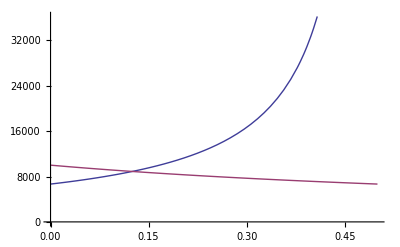

```mathematica
Plot[{b,c},{nu,0,0.5},AxesOrigin->{0,0}]
```

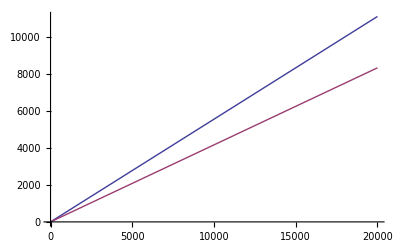

```mathematica
Plot[{bb,cc},{e,0,20000}]
```